```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
pointList = Import["llpLifetimePoints.csv"];
pointTable = Table[{pointList[[i,1]],pointList[[i,2]]},{i,1,Length[pointList]}];
```

```mathematica
pointTable
```

{{0.0858058,45.9172},{0.0964986,40.837},{0.108524,36.1167},{0.122048,32.1208},{0.137257,28.727},{0.154361,25.1945},{0.173597,22.5325},{0.195229,19.7618},{0.210379,14.2155},{0.210829,6.5566},{0.212637,3.68088},{0.213775,1.73462},{0.2141,0.889477},{0.21607,0.385224},{0.215379,0.187199},{0.217226,0.0923766},{0.217691,0.0447527},{0.220969,0.0188247},{0.228788,0.00741409},{0.241333,0.00342561},{0.260457,0.001774},{0.275915,0.000878491},{0.283681,0.00037486},{0.304067,0.000181233},{0.336526,0.000100839},{0.378462,0.0000593295},{0.425624,0.0000375348},{0.478664,0.0000249702},{0.538313,0.0000178621},{0.605395,0.0000128848},{0.680836,9.69198×10^-6},{0.765679,6.72336×10^-6},{0.847414,3.85624×10^-6},{0.90831,1.92497×10^-6},{0.965303,7.87643×10^-7},{1.03404,6.60008×10^-7},{1.14879,1.37316×10^-6},{1.29195,2.77492×10^-6},{1.45295,3.39269×10^-6},{1.63401,2.39327×10^-6},{1.83763,1.67418×10^-6},{2.06663,1.16139×10^-6},{2.32416,8.07909×10^-7},{2.61379,5.95949×10^-7},{2.87741,3.96774×10^-7},{3.10069,1.86571×10^-7},{3.41341,1.04682×10^-7},{3.83878,6.81023×10^-8},{4.31715,4.92631×10^-8},{4.85513,3.82113×10^-8},{5.46016,3.12534×10^-8},{6.14058,2.6067×10^-8},{6.90579,2.19853×10^-8},{7.76635,1.8856×10^-8},{8.73416,1.59926×10^-8},{9.66652,1.17639×10^-8},{10.5284,5.52254×10^-9},{11.6523,3.04609×10^-9},{13.1044,2.03209×10^-9},{14.7374,1.58946×10^-9},{16.5739,1.32569×10^-9},{18.6393,1.137×10^-9},{20.962,1.00557×10^-9},{23.5742,9.0184×10^-10},{26.5119,8.11069×10^-10},{29.8157,7.31473×10^-10},{33.5312,6.67096×10^-10},{37.7097,6.03311×10^-10},{42.4089,5.4868×10^-10},{47.6937,4.97605×10^-10},{53.6371,4.50026×10^-10},{59.0468,4.13871×10^-10}}

```mathematica
intLT = Interpolation[pointTable,InterpolationOrder->1]
```

InterpolatingFunction[…]

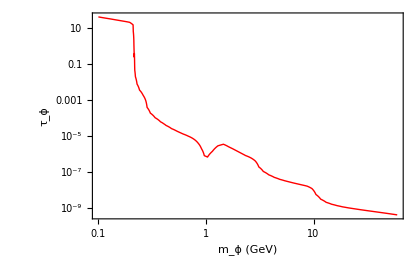

```mathematica
LogLogPlot[intLT[mPhi],{mPhi,10^(-1),60},FrameLabel->{"m_ϕ (GeV)","τ_ϕ"},Frame->True,LabelStyle->{Black,15},ImageSize->420,PlotStyle->Directive[Red,Thick]]
```

```mathematica
tauPhiTest[mPhi_] := 10^(-1.116*Log[10,mPhi]+0.4777);
```

```mathematica
mPhi = 1;
intLT[mPhi]
tauPhiTest[mPhi]
If[mPhi ≤ 0.2,tauPhiPlot = 10^(-1.116*Log[10,mPhi]+0.4777), tauPhiPlot = intLT[mPhi]];
tauPhiPlot
```

7.23216×10^-7

3.004

7.23216×10^-7